### Code (new method of calling new header)

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

### Tests

Select a ruleset to investigate, possibly by giving its reduced rank index, giving it some convenient name:

```mathematica
rs=FromReducedRankIndex[702927424475]
```

<|Index→702927424475,QCode→31342432243424233,RuleSet→{AA→,AB→BA,A→BB,B→AAA}|>

We generate the sessie and its causal network, again giving it a convenient name:



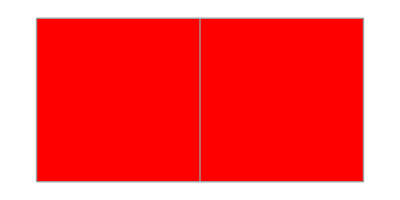

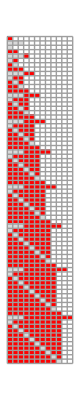
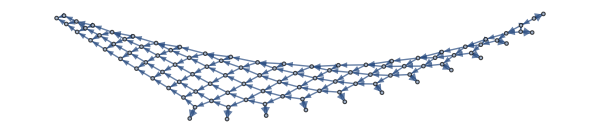
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss=SSS[rs[["RuleSet"]], "B",1000, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->75,NetMax->100,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic]; (* options can be changed or omitted, but these are reasonable choices *)
```

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss[["Net"]]//Short
```

{1→2,1→2,1→3,3→4,4→5,4→5,4→6,3→6,6→7,6→8,«1894»,995→996,953→996,996→997,954→997,997→998,955→998,998→999,956→999,999→1000,957→1000}

```mathematica
nds=ToNetDifferenceSets[sss[["Net"]]]
```

{{1,1,2},{},{1,3},{1,1,2},{},{1,2},{3,4},{1,1,2},{},{1,3},{1,4},{4,5},{1,1,2},{},{1,4},{1,5},{1,5},{5,6},{1,1,2},{},{1,5},{1,6},{1,6},{1,6},{6,7},{1,1,2},{},{1,6},{1,7},{1,7},{1,7},{1,7},{7,8},{1,1,2},{},{1,7},{1,8},{1,8},{1,8},{1,8},{1,8},{8,9},{1,1,2},{},{1,8},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{9,10},{1,1,2},{},{1,9},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10,11},{1,1,2},{},{1,10},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11,12},{1,1,2},{},{1,11},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12,13},{1,1,2},{},{1,12},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{13,14},{1,1,2},{},{1,13},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{14,15},{1,1,2},{},{1,14},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{15,16},{1,1,2},{},{1,15},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{16,17},{1,1,2},{},{1,16},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{17,18},{1,1,2},{},{1,17},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{18,19},{1,1,2},{},{1,18},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{19,20},{1,1,2},{},{1,19},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{20,21},{1,1,2},{},{1,20},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{21,22},{1,1,2},{},{1,21},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{22,23},{1,1,2},{},{1,22},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{23,24},{1,1,2},{},{1,23},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{24,25},{1,1,2},{},{1,24},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{25,26},{1,1,2},{},{1,25},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{26,27},{1,1,2},{},{1,26},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{27,28},{1,1,2},{},{1,27},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{28,29},{1,1,2},{},{1,28},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{29,30},{1,1,2},{},{1,29},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{30,31},{1,1,2},{},{1,30},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{31,32},{1,1,2},{},{1,31},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{32,33},{1,1,2},{},{1,32},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{33,34},{1,1,2},{},{1,33},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{34,35},{1,1,2},{},{1,34},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{35,36},{1,1,2},{},{1,35},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{36,37},{1,1,2},{},{1,36},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{37,38},{1,1,2},{},{1,37},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{38,39},{1,1,2},{},{1,38},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{39,40},{1,1,2},{},{1,39},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{40,41},{1,1,2},{},{1,40},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{41,42},{1,1,2},{},{1,41},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{42,43},{1,1,2},{},{1,42},{1,43},{1,43},{1,43},{1,43},{1,43},{1,43},{1,43},{1,43},{1,43},{1,43},{1,43},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{},{1,1,2},{},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

You will probably need to limit the part of the nds list that you try to compact, omitting the incomplete sets at the end of the list. In theory it’s not needed to start later than the beginning of the list.

```mathematica
Position[nds,{42,43}]
```

{{943}}

```mathematica
nds[[1;;943]]
```

{{1,1,2},{},{1,3},{1,1,2},{},{1,2},{3,4},{1,1,2},{},{1,3},{1,4},{4,5},{1,1,2},{},{1,4},{1,5},{1,5},{5,6},{1,1,2},{},{1,5},{1,6},{1,6},{1,6},{6,7},{1,1,2},{},{1,6},{1,7},{1,7},{1,7},{1,7},{7,8},{1,1,2},{},{1,7},{1,8},{1,8},{1,8},{1,8},{1,8},{8,9},{1,1,2},{},{1,8},{1,9},{1,9},{1,9},{1,9},{1,9},{1,9},{9,10},{1,1,2},{},{1,9},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{1,10},{10,11},{1,1,2},{},{1,10},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{1,11},{11,12},{1,1,2},{},{1,11},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{1,12},{12,13},{1,1,2},{},{1,12},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{1,13},{13,14},{1,1,2},{},{1,13},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{1,14},{14,15},{1,1,2},{},{1,14},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{1,15},{15,16},{1,1,2},{},{1,15},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{1,16},{16,17},{1,1,2},{},{1,16},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{1,17},{17,18},{1,1,2},{},{1,17},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{1,18},{18,19},{1,1,2},{},{1,18},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{1,19},{19,20},{1,1,2},{},{1,19},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{1,20},{20,21},{1,1,2},{},{1,20},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{1,21},{21,22},{1,1,2},{},{1,21},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{1,22},{22,23},{1,1,2},{},{1,22},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{1,23},{23,24},{1,1,2},{},{1,23},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{1,24},{24,25},{1,1,2},{},{1,24},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{1,25},{25,26},{1,1,2},{},{1,25},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{1,26},{26,27},{1,1,2},{},{1,26},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{1,27},{27,28},{1,1,2},{},{1,27},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{1,28},{28,29},{1,1,2},{},{1,28},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{1,29},{29,30},{1,1,2},{},{1,29},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{1,30},{30,31},{1,1,2},{},{1,30},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{1,31},{31,32},{1,1,2},{},{1,31},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{1,32},{32,33},{1,1,2},{},{1,32},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{1,33},{33,34},{1,1,2},{},{1,33},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{1,34},{34,35},{1,1,2},{},{1,34},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{1,35},{35,36},{1,1,2},{},{1,35},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{1,36},{36,37},{1,1,2},{},{1,36},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{1,37},{37,38},{1,1,2},{},{1,37},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{1,38},{38,39},{1,1,2},{},{1,38},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{1,39},{39,40},{1,1,2},{},{1,39},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{1,40},{40,41},{1,1,2},{},{1,40},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{1,41},{41,42},{1,1,2},{},{1,41},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{1,42},{42,43}}

Try the reduction:

```mathematica
rsl=ReduceSetList[nds[[1;;943]]]
```

{€_(n$2⊨1)^2[{1,1,2},{},{1,4-n$2}],{3,4},{1,1,2},{},€_(n$1⊨1)^2[{1,2+n$1}],€_(n$3⊨1)^38[{3+n$3,4+n$3},{1,1,2},{},{1,3+n$3},€^(1+n$3)[{1,4+n$3}]],{42,43}}

Hurrah!

```mathematica
rsl[[-2]]/.n$3->k
```

€_(k⊨1)^38[{k+3,k+4},{1,1,2},{},{1,k+3},€^(k+1)[{1,k+4}]]

```mathematica
rsl[[-2]]/.n$3->k//InputForm
```

IndexedConcatenate[{3 + k, 4 + k}, {1, 1, 2}, {}, {1, 3 + k}, IndexedConcatenate[{1, 4 + k}, 1 + k], {k, 1, 38}]

Can we do better?

```mathematica
{ExpandAll[%]}
```

```mathematica
GraphPlot[FromNetDifferenceSets@%]
```